```mathematica
Directory[]
```

/home/cmaier/scad/Maerklin/analysis

```mathematica
Dimensions[raw=Import["TTL.10ms.5V.csv"]]
```

{524290,4}

```mathematica
Take[raw,5]
```

{{X,CH1,CH2,},{Second,Volt,Volt,},{-0.131112,5.4,0.,},{-0.131112,5.4,0.,},{-0.131111,5.4,0.,}}

```mathematica
Dimensions[timeseries=Transpose[{{#⟦1⟧,#⟦2⟧},{#⟦1⟧,#⟦3⟧}}&/@Drop[raw,2],{2,1,3}]]
```

{2,524288,2}

```mathematica
ListPlot[Take[#,{55000,155000}]&/@timeseries,Frame->True,Joined->True]
```

-Graphics-

```mathematica
Dimensions[digitized=Map[{#⟦1⟧,HeavisideTheta[#⟦2⟧-3]}&,timeseries,{2}]]
```

{2,524288,2}

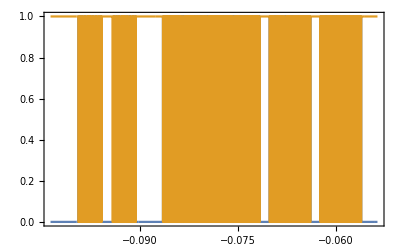

```mathematica
ListPlot[Take[#,{55000,155000}]&/@digitized,Frame->True,Joined->True]
```

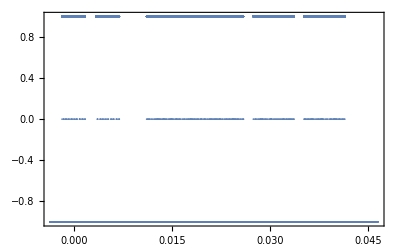

```mathematica
ListPlot[Take[MapThread[{(#1⟦1⟧+#2⟦1⟧)/2,#1⟦2⟧-#2⟦2⟧}&,digitized],{255000,355000}],Frame->True,Joined->False]
```

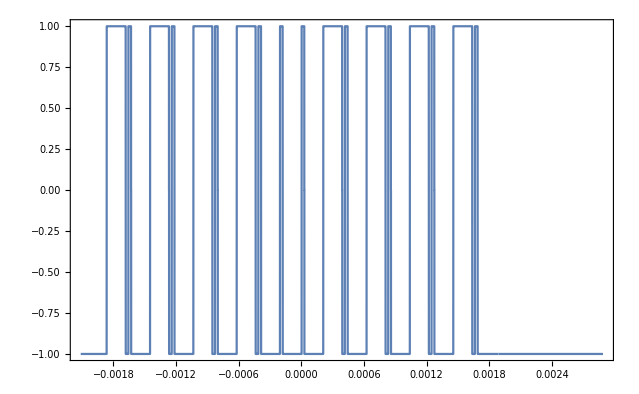

```mathematica
ListPlot[Take[MapThread[{(#1⟦1⟧+#2⟦1⟧)/2,#1⟦2⟧-#2⟦2⟧}&,digitized],{258000,268000}],Frame->True,Joined->True]
```

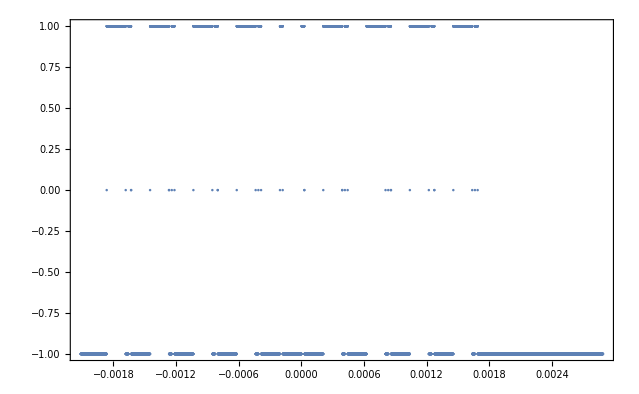

```mathematica
ListPlot[Take[MapThread[{(#1⟦1⟧+#2⟦1⟧)/2,#1⟦2⟧-#2⟦2⟧}&,digitized],{258000,268000}],Frame->True,Joined->False]
```